```mathematica
Clear[v2,v3]
```

```mathematica
k={-1,1/v1,1/v2,1/v3}
k={-1,k1,k2,k3}
u={uu0,uu1,uu2,uu3}
gcon={{g00,g01,g02,g03},{g01,g11,g12,g13},{g02,g12,g22,g23},{g03,g13,g23,g33}}
MatrixForm[gcon]
```

{-1,1/v1,1/v2,1/v3}

{-1,k1,k2,k3}

{uu0,uu1,uu2,uu3}

{{g00,g01,g02,g03},{g01,g11,g12,g13},{g02,g12,g22,g23},{g03,g13,g23,g33}}

(g00 | g01 | g02 | g03
g01 | g11 | g12 | g13
g02 | g12 | g22 | g23
g03 | g13 | g23 | g33)

```mathematica
eq1=FullSimplify[A==(k.u)^2/(k.gcon.k)]
```

A==(-uu0+k1 uu1+k2 uu2+k3 uu3)^2/(g00-2 g01 k1+g11 k1^2+2 g12 k1 k2+g22 k2^2-2 (g02 k2+g03 k3)+k3 (2 g13 k1+2 g23 k2+g33 k3))

```mathematica
sols=Solve[eq1,k1]
```

{{k1→1/(2 (A g11-uu1^2))(2 A g01-2 A g12 k2-2 A g13 k3-2 uu0 uu1+2 k2 uu1 uu2+2 k3 uu1 uu3-√((-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)^2-4 (A g11-uu1^2) (A g00-2 A g02 k2+A g22 k2^2-2 A g03 k3+2 A g23 k2 k3+A g33 k3^2-uu0^2+2 k2 uu0 uu2-k2^2 uu2^2+2 k3 uu0 uu3-2 k2 k3 uu2 uu3-k3^2 uu3^2)))},{k1→1/(2 (A g11-uu1^2))(2 A g01-2 A g12 k2-2 A g13 k3-2 uu0 uu1+2 k2 uu1 uu2+2 k3 uu1 uu3+√((-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)^2-4 (A g11-uu1^2) (A g00-2 A g02 k2+A g22 k2^2-2 A g03 k3+2 A g23 k2 k3+A g33 k3^2-uu0^2+2 k2 uu0 uu2-k2^2 uu2^2+2 k3 uu0 uu3-2 k2 k3 uu2 uu3-k3^2 uu3^2)))}}

```mathematica
sol1=sols[[1,1,2]]
```

1/(2 (A g11-uu1^2))(2 A g01-2 A g12 k2-2 A g13 k3-2 uu0 uu1+2 k2 uu1 uu2+2 k3 uu1 uu3-√((-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)^2-4 (A g11-uu1^2) (A g00-2 A g02 k2+A g22 k2^2-2 A g03 k3+2 A g23 k2 k3+A g33 k3^2-uu0^2+2 k2 uu0 uu2-k2^2 uu2^2+2 k3 uu0 uu3-2 k2 k3 uu2 uu3-k3^2 uu3^2)))

```mathematica
con1=D[sol1,k2]
con2=D[sol1,k3]
Solve[{con1==0,con2==0},{k2,k3}]
```

1/(2 (A g11-uu1^2))(-2 A g12+2 uu1 uu2-(2 (2 A g12-2 uu1 uu2) (-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)-4 (A g11-uu1^2) (-2 A g02+2 A g22 k2+2 A g23 k3+2 uu0 uu2-2 k2 uu2^2-2 k3 uu2 uu3))/(2 √((-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)^2-4 (A g11-uu1^2) (A g00-2 A g02 k2+A g22 k2^2-2 A g03 k3+2 A g23 k2 k3+A g33 k3^2-uu0^2+2 k2 uu0 uu2-k2^2 uu2^2+2 k3 uu0 uu3-2 k2 k3 uu2 uu3-k3^2 uu3^2))))

1/(2 (A g11-uu1^2))(-2 A g13+2 uu1 uu3-(2 (2 A g13-2 uu1 uu3) (-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)-4 (A g11-uu1^2) (-2 A g03+2 A g23 k2+2 A g33 k3+2 uu0 uu3-2 k2 uu2 uu3-2 k3 uu3^2))/(2 √((-2 A g01+2 A g12 k2+2 A g13 k3+2 uu0 uu1-2 k2 uu1 uu2-2 k3 uu1 uu3)^2-4 (A g11-uu1^2) (A g00-2 A g02 k2+A g22 k2^2-2 A g03 k3+2 A g23 k2 k3+A g33 k3^2-uu0^2+2 k2 uu0 uu2-k2^2 uu2^2+2 k3 uu0 uu3-2 k2 k3 uu2 uu3-k3^2 uu3^2))))

Hold[Abort[],Abort[]]

```mathematica
k={kd0,kd1,kd2,kd3}
u={uu0,uu1,uu2,uu3}
ksq=k.gcon.k
omega=-k.u
Ksq=ksq+omega^2
Disp=omega^2-a^2*Ksq
```

{kd0,kd1,kd2,kd3}

{uu0,uu1,uu2,uu3}

kd0 (g00 kd0+g01 kd1+g02 kd2+g03 kd3)+kd1 (g01 kd0+g11 kd1+g12 kd2+g13 kd3)+kd2 (g02 kd0+g12 kd1+g22 kd2+g23 kd3)+kd3 (g03 kd0+g13 kd1+g23 kd2+g33 kd3)

-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3

kd0 (g00 kd0+g01 kd1+g02 kd2+g03 kd3)+kd1 (g01 kd0+g11 kd1+g12 kd2+g13 kd3)+kd2 (g02 kd0+g12 kd1+g22 kd2+g23 kd3)+kd3 (g03 kd0+g13 kd1+g23 kd2+g33 kd3)+(-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)^2

(-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)^2-a^2 (kd0 (g00 kd0+g01 kd1+g02 kd2+g03 kd3)+kd1 (g01 kd0+g11 kd1+g12 kd2+g13 kd3)+kd2 (g02 kd0+g12 kd1+g22 kd2+g23 kd3)+kd3 (g03 kd0+g13 kd1+g23 kd2+g33 kd3)+(-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)^2)

```mathematica
hg={D[Disp,kd0],D[Disp,kd1],D[Disp,kd2],D[Disp,kd3]}
```

{-2 uu0 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)-a^2 (2 g00 kd0+2 g01 kd1+2 g02 kd2+2 g03 kd3-2 uu0 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)),-2 uu1 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)-a^2 (2 g01 kd0+2 g11 kd1+2 g12 kd2+2 g13 kd3-2 uu1 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)),-2 uu2 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)-a^2 (2 g02 kd0+2 g12 kd1+2 g22 kd2+2 g23 kd3-2 uu2 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)),-2 uu3 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3)-a^2 (2 g03 kd0+2 g13 kd1+2 g23 kd2+2 g33 kd3-2 uu3 (-kd0 uu0-kd1 uu1-kd2 uu2-kd3 uu3))}

```mathematica
sols=Solve[Disp==0,kd0]
sol1=sols[[1,1,2]]
```

{{kd0→1/(2 (-a^2 g00+uu0^2-a^2 uu0^2))(2 a^2 g01 kd1+2 a^2 g02 kd2+2 a^2 g03 kd3-2 kd1 uu0 uu1+2 a^2 kd1 uu0 uu1-2 kd2 uu0 uu2+2 a^2 kd2 uu0 uu2-2 kd3 uu0 uu3+2 a^2 kd3 uu0 uu3-√((-2 a^2 g01 kd1-2 a^2 g02 kd2-2 a^2 g03 kd3+2 kd1 uu0 uu1-2 a^2 kd1 uu0 uu1+2 kd2 uu0 uu2-2 a^2 kd2 uu0 uu2+2 kd3 uu0 uu3-2 a^2 kd3 uu0 uu3)^2-4 (-a^2 g00+uu0^2-a^2 uu0^2) (-a^2 g11 kd1^2-2 a^2 g12 kd1 kd2-a^2 g22 kd2^2-2 a^2 g13 kd1 kd3-2 a^2 g23 kd2 kd3-a^2 g33 kd3^2+kd1^2 uu1^2-a^2 kd1^2 uu1^2+2 kd1 kd2 uu1 uu2-2 a^2 kd1 kd2 uu1 uu2+kd2^2 uu2^2-a^2 kd2^2 uu2^2+2 kd1 kd3 uu1 uu3-2 a^2 kd1 kd3 uu1 uu3+2 kd2 kd3 uu2 uu3-2 a^2 kd2 kd3 uu2 uu3+kd3^2 uu3^2-a^2 kd3^2 uu3^2)))},{kd0→1/(2 (-a^2 g00+uu0^2-a^2 uu0^2))(2 a^2 g01 kd1+2 a^2 g02 kd2+2 a^2 g03 kd3-2 kd1 uu0 uu1+2 a^2 kd1 uu0 uu1-2 kd2 uu0 uu2+2 a^2 kd2 uu0 uu2-2 kd3 uu0 uu3+2 a^2 kd3 uu0 uu3+√((-2 a^2 g01 kd1-2 a^2 g02 kd2-2 a^2 g03 kd3+2 kd1 uu0 uu1-2 a^2 kd1 uu0 uu1+2 kd2 uu0 uu2-2 a^2 kd2 uu0 uu2+2 kd3 uu0 uu3-2 a^2 kd3 uu0 uu3)^2-4 (-a^2 g00+uu0^2-a^2 uu0^2) (-a^2 g11 kd1^2-2 a^2 g12 kd1 kd2-a^2 g22 kd2^2-2 a^2 g13 kd1 kd3-2 a^2 g23 kd2 kd3-a^2 g33 kd3^2+kd1^2 uu1^2-a^2 kd1^2 uu1^2+2 kd1 kd2 uu1 uu2-2 a^2 kd1 kd2 uu1 uu2+kd2^2 uu2^2-a^2 kd2^2 uu2^2+2 kd1 kd3 uu1 uu3-2 a^2 kd1 kd3 uu1 uu3+2 kd2 kd3 uu2 uu3-2 a^2 kd2 kd3 uu2 uu3+kd3^2 uu3^2-a^2 kd3^2 uu3^2)))}}

1/(2 (-a^2 g00+uu0^2-a^2 uu0^2))(2 a^2 g01 kd1+2 a^2 g02 kd2+2 a^2 g03 kd3-2 kd1 uu0 uu1+2 a^2 kd1 uu0 uu1-2 kd2 uu0 uu2+2 a^2 kd2 uu0 uu2-2 kd3 uu0 uu3+2 a^2 kd3 uu0 uu3-√((-2 a^2 g01 kd1-2 a^2 g02 kd2-2 a^2 g03 kd3+2 kd1 uu0 uu1-2 a^2 kd1 uu0 uu1+2 kd2 uu0 uu2-2 a^2 kd2 uu0 uu2+2 kd3 uu0 uu3-2 a^2 kd3 uu0 uu3)^2-4 (-a^2 g00+uu0^2-a^2 uu0^2) (-a^2 g11 kd1^2-2 a^2 g12 kd1 kd2-a^2 g22 kd2^2-2 a^2 g13 kd1 kd3-2 a^2 g23 kd2 kd3-a^2 g33 kd3^2+kd1^2 uu1^2-a^2 kd1^2 uu1^2+2 kd1 kd2 uu1 uu2-2 a^2 kd1 kd2 uu1 uu2+kd2^2 uu2^2-a^2 kd2^2 uu2^2+2 kd1 kd3 uu1 uu3-2 a^2 kd1 kd3 uu1 uu3+2 kd2 kd3 uu2 uu3-2 a^2 kd2 kd3 uu2 uu3+kd3^2 uu3^2-a^2 kd3^2 uu3^2)))

```mathematica
Simplify[(hg.hg)//.{kd0->sol1}]
```

$Aborted

```mathematica
Solve[-2*a^2+3*a^4-2*a^6==0.,a]
```

{{a→-0.935414-0.353553 ⅈ},{a→-0.935414+0.353553 ⅈ},{a→0.},{a→0.},{a→0.935414-0.353553 ⅈ},{a→0.935414+0.353553 ⅈ}}

```mathematica
phase=a/Sqrt[1-a^2]
D[phase,a]
```

a/(√(1-a^2))

a^2/((1-a^2)^(3/2))+1/(√(1-a^2))

```mathematica
Solve[phase==1,a]
```

{{a→1/(√2)}}

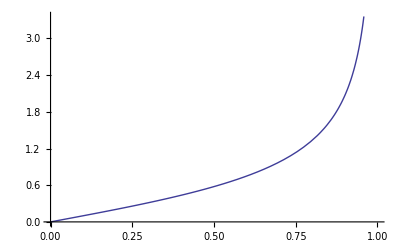

```mathematica
Plot[phase,{a,0,1}]
```

```mathematica
ksq
```

kd0 (g00 kd0+g01 kd1+g02 kd2+g03 kd3)+kd1 (g01 kd0+g11 kd1+g12 kd2+g13 kd3)+kd2 (g02 kd0+g12 kd1+g22 kd2+g23 kd3)+kd3 (g03 kd0+g13 kd1+g23 kd2+g33 kd3)

```mathematica
kd=k
```

{kd0,kd1,kd2,kd3}

```mathematica
ku=k.gcon
```

{g00 kd0+g01 kd1+g02 kd2+g03 kd3,g01 kd0+g11 kd1+g12 kd2+g13 kd3,g02 kd0+g12 kd1+g22 kd2+g23 kd3,g03 kd0+g13 kd1+g23 kd2+g33 kd3}

```mathematica
eq1=0==-ku[[1]]*kd[[2]]/ksq//.{g03->0,g02->0,g01->0,g23->0,g13->0,g12->0}
eq2=0==1-ku[[2]]*kd[[2]]/ksq//.{g03->0,g02->0,g01->0,g23->0,g13->0,g12->0}
eq3=0==-ku[[3]]*kd[[2]]/ksq//.{g03->0,g02->0,g01->0,g23->0,g13->0,g12->0}
eq4=0==-ku[[4]]*kd[[2]]/ksq//.{g03->0,g02->0,g01->0,g23->0,g13->0,g12->0}
```

0==-(g00 kd0 kd1)/(g00 kd0^2+g11 kd1^2+g22 kd2^2+g33 kd3^2)

0==1-(g11 kd1^2)/(g00 kd0^2+g11 kd1^2+g22 kd2^2+g33 kd3^2)

0==-(g22 kd1 kd2)/(g00 kd0^2+g11 kd1^2+g22 kd2^2+g33 kd3^2)

0==-(g33 kd1 kd3)/(g00 kd0^2+g11 kd1^2+g22 kd2^2+g33 kd3^2)

```mathematica
sols=FullSimplify[Solve[{eq2,eq3,eq4},{kd1,kd2,kd3}]]
```

{}

```mathematica
FullSimplify[sols//.{g03->0,g02->0,g01->0,g23->0,g13->0}]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0\ kd3\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

{{kd1→ComplexInfinity,kd0→Indeterminate,kd2→ComplexInfinity}}

```mathematica
a*Sqrt[1-a^2]//.{a->1/Sqrt[2]}
```

1/2

```mathematica
Plot[
```